```mathematica
LJ[x_]=1/x^12-1/x^6;
```

```mathematica
bondLength=ArgMin[{LJ[x],x>0},x];
```

```mathematica
hooke[x_]=x^2;
```

```mathematica
bondLength
```

2^(1/6)

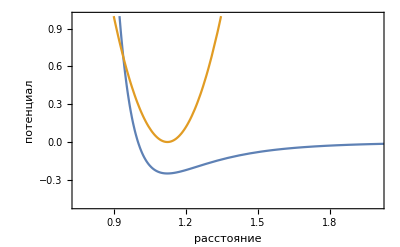

```mathematica
Plot[
{LJ[x],20hooke[x-bondLength]},
{x,0,2bondLength},
PlotRange->{{3/4,2},{-1/2,1}},
FrameLabel->{"расстояние","потенциал"},
Frame->True
]
```